### Dynamical Systems TIF155/FIM770 Konstantinos Zakkas Problem set 2

### 2.2 Damped pendulum e)

```mathematica
xDot[x_,y_,σ_]:=y
yDot[x_,y_,σ_]:=-Sin[x]-σ y
Table[StreamPlot[{xDot[x,y,σ],yDot[x,y,σ]},{x,-π,π}, {y,-5,5}],{σ,{0,0.5,1,2,5,10}}];
```

```mathematica
Solve[{xDot[x,y,σ] == 0, yDot[x,y,σ]==0}]
```

{{y→0,x→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{y→0,x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

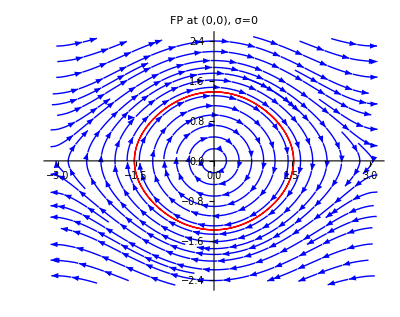

```mathematica
stream = Table[StreamPlot[{xDot[x,y,σ],yDot[x,y,σ]},{x,-π,π},{y,-2.5,2.5},StreamStyle->{Blue},StreamColorFunction->None],{σ,{0}}];
sols=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==1,y[0]==1},{x[t],y[t]},{t,0,15}],{σ,{0}}];
funcs={x[t],y[t]}/.sols;
p=ParametricPlot[funcs,{t,0,15},PlotRange->All, PlotStyle->{Red, Thick}, PlotLabel->"FP at (0,0), σ=0"];
Show[{p, stream}]
(*Center at {0,0}*)
```

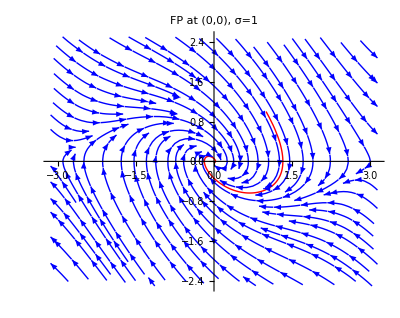

```mathematica
stream = Table[StreamPlot[{xDot[x,y,σ],yDot[x,y,σ]},{x,-π,π},{y,-2.5,2.5},StreamStyle->{Blue},StreamColorFunction->None],{σ,{1}}];
sols=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==1,y[0]==1},{x[t],y[t]},{t,0,15}],{σ,{1}}];
funcs={x[t],y[t]}/.sols;
p=ParametricPlot[funcs,{t,0,15},PlotRange->All, PlotStyle->{Red, Thick}, PlotLabel->"FP at (0,0), σ=1"];
Show[{p, stream}]
(*Stable spiral*)
```

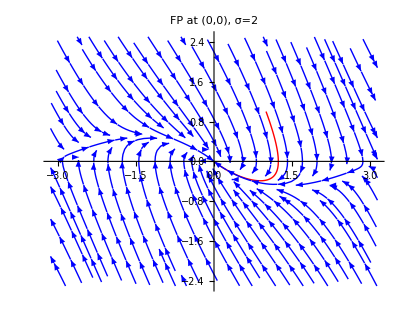

```mathematica
stream = Table[StreamPlot[{xDot[x,y,σ],yDot[x,y,σ]},{x,-π,π},{y,-2.5,2.5},StreamStyle->{Blue},StreamColorFunction->None],{σ,{2}}];
sols=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==1,y[0]==1},{x[t],y[t]},{t,0,15}],{σ,{2}}];
funcs={x[t],y[t]}/.sols;
p=ParametricPlot[funcs,{t,0,15},PlotRange->All, PlotStyle->{Red, Thick}, PlotLabel->"FP at (0,0), σ=2"];
Show[{p, stream}]
(*Bifurcation point from stable spiral to stalbe node*)
```

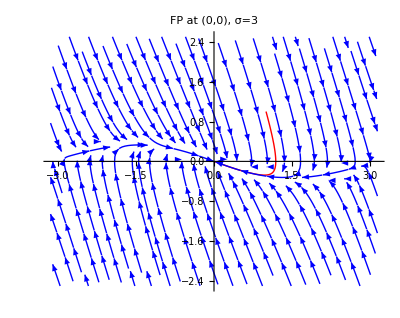

```mathematica
stream = Table[StreamPlot[{xDot[x,y,σ],yDot[x,y,σ]},{x,-π,π},{y,-2.5,2.5},StreamStyle->{Blue},StreamColorFunction->None],{σ,{3}}];
sols=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==1,y[0]==1},{x[t],y[t]},{t,0,15}],{σ,{3}}];
funcs={x[t],y[t]}/.sols;
p=ParametricPlot[funcs,{t,0,15},PlotRange->All, PlotStyle->{Red, Thick}, PlotLabel->"FP at (0,0), σ=3"];
Show[{p, stream}]
(*Stable node*)
```

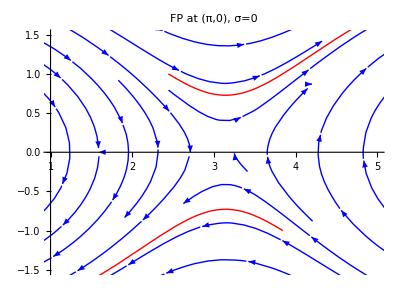

```mathematica
sols=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==π-0.7,y[0]==1},{x[t],y[t]},{t,0,10}],{σ,{0}}];
funcs={x[t],y[t]}/.sols;
p1=ParametricPlot[funcs,{t,0,10}, PlotRange->{{1,5},{-1.5,1.5}},
PlotStyle->{Red,Thick},
PlotLabel->"FP at (π,0), σ=0"];
sols=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==π+0.7,y[0]==-1},{x[t],y[t]},{t,0,10}],{σ,{0}}];
funcs={x[t],y[t]}/.sols;
p2=ParametricPlot[funcs,{t,0,10}, PlotRange->{{1,5},{-1.5,1.5}},
PlotStyle->{Red,Thick}];
p3 = stream = Table[StreamPlot[{xDot[x,y,σ],yDot[x,y,σ]},{x,-2π,2π},{y,-2.5,2.5},StreamStyle->{Blue},StreamColorFunction->None],{σ,{0}}];
Show[{p1,p2, p3}]
(*Saddle node*)
```

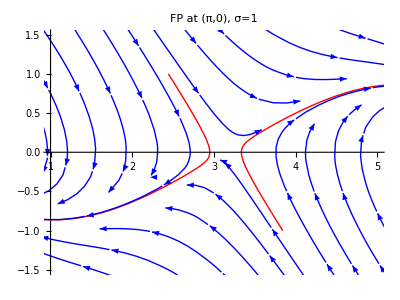

```mathematica
sols=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==π-0.7,y[0]==1},{x[t],y[t]},{t,0,10}],{σ,{1}}];
funcs={x[t],y[t]}/.sols;
p1=ParametricPlot[funcs,{t,0,10}, PlotRange->{{1,5},{-1.5,1.5}},
PlotStyle->{Red,Thick},
PlotLabel->"FP at (π,0), σ=1"];
sols=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==π+0.7,y[0]==-1},{x[t],y[t]},{t,0,10}],{σ,{1}}];
funcs={x[t],y[t]}/.sols;
p2=ParametricPlot[funcs,{t,0,10}, PlotRange->{{1,5},{-1.5,1.5}},
PlotStyle->{Red,Thick}];
p3 = stream = Table[StreamPlot[{xDot[x,y,σ],yDot[x,y,σ]},{x,-2π,2π},{y,-2.5,2.5},StreamStyle->{Blue},StreamColorFunction->None],{σ,{1}}];
Show[{p1,p2, p3}]
(*Saddle node*)
```

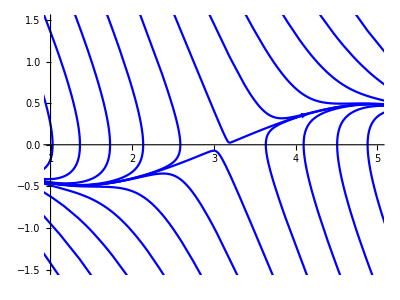

```mathematica
sols=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==π-0.7,y[0]==1},{x[t],y[t]},{t,0,10}],{σ,{2}}];
funcs={x[t],y[t]}/.sols;
p1=ParametricPlot[funcs,{t,0,10}, PlotRange->{{1,5},{-1.5,1.5}},
PlotStyle->{Red,Thick},
PlotLabel->"FP at (π,0), σ=2"];
sols=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==π+0.7,y[0]==-1},{x[t],y[t]},{t,0,10}],{σ,{2}}];
inits=Join[Table[{-2π,y},{y,-2.5,2.5,0.4}],Table[{2π,y},{y,-2.5,2.5,0.4}],Table[{x,-2.5},{x,-2π,2π,0.4}],Table[{x,2.5},{x,-2π,2π,0.4}]];
funcs={x[t],y[t]};
p2=Table[ParametricPlot[Evaluate[funcs/.sol[inits[[i,1]],inits[[i,2]]]],{t,0,10}, PlotRange->{{1,5},{-1.5,1.5}},
PlotStyle->{Blue}]/.Line[x_]:>{Arrowheads[{0.,0.05,0.05,0.05,0.}],Arrow[x]},{i,Length[inits]}];
p3 = stream = Table[StreamPlot[{xDot[x,y,σ],yDot[x,y,σ]},{x,-2π,2π},{y,-2.5,2.5},StreamStyle->{Blue},StreamColorFunction->None],{σ,{2}}];
Show[{p2}]
(*Saddle node*)
```

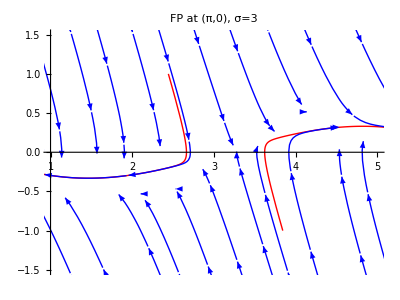

```mathematica
sols=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==π-0.7,y[0]==1},{x[t],y[t]},{t,0,10}],{σ,{3}}];
funcs={x[t],y[t]}/.sols;
p1=ParametricPlot[funcs,{t,0,10}, PlotRange->{{1,5},{-1.5,1.5}},
PlotStyle->{Red,Thick},
PlotLabel->"FP at (π,0), σ=3"];
sols=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==π+0.7,y[0]==-1},{x[t],y[t]},{t,0,10}],{σ,{3}}];
funcs={x[t],y[t]}/.sols;
p2=ParametricPlot[funcs,{t,0,10}, PlotRange->{{1,5},{-1.5,1.5}},
PlotStyle->{Red,Thick}];
p3 = stream = Table[StreamPlot[{xDot[x,y,σ],yDot[x,y,σ]},{x,-2π,2π},{y,-2.5,2.5},StreamStyle->{Blue},StreamColorFunction->None],{σ,{3}}];
Show[{p1,p2, p3}]
(*Saddle node*)
```